```mathematica
NotebookEvaluate[NotebookDirectory[]<>"/split_step.nb"];
```

GPE solver v1.4, RZ 2019

```mathematica
HarmonicTrap1D[];
sizes={4096};
timeStep=0.00025;
k=-0.5;
contactInteractionFactor=4 Pi k;
max=50ho;
min=-50ho;
initialize[];
gridReport
```

sizes | dim | len | max | min | delta | deltak | maxk
{4096} | 1 | 4096 | {50} | {-50} | {20/819} | {(819 π)/40960} | {(819 π)/20}

```mathematica
calcAllTable
p1=plotProjections;
```

time | energies | moments | misc
(0) | (total | -0.753314
kinetic | 0.25
potential | 0.25
contact | -1.25331
virial | -1.25331) | (meanX | 0
sigmaX | 0.707107
norm | 1.) | (steps | 0
A0 | 0.751126)

```mathematica
AbsoluteTiming[evolve["ite",10,10]]
```

{29.4991,Null}

time | energies | moments | misc
(10.) | (total | -1.60446
kinetic | 1.71707
potential | 0.0394871
contact | -3.36102
virial | -0.0058447) | (meanX | 0
sigmaX | 0.281024
norm | 1.) | (steps | 40000
A0 | 1.26515)

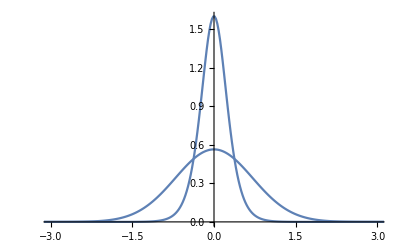

```mathematica
calcAllTable
p2=plotProjections;
Show[p1,p2,PlotRange->{{-3,3},All}]
```

Turn off harmonic potential

```mathematica
plot:=AppendTo[lplots,{time,plotProjections,interp[wf]}];
newPotential[(0&)];
reset;
AbsoluteTiming[evolve["ite",10,10,10]]
```

{29.7334,Null}

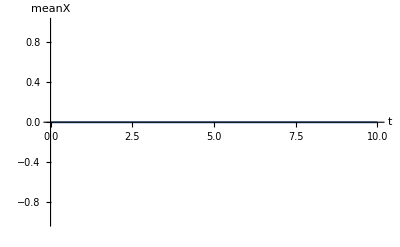
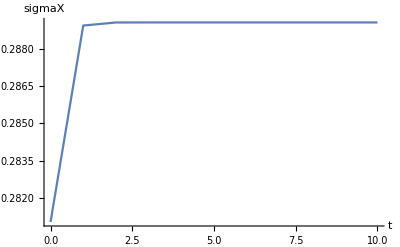

```mathematica
{plotM["meanX"],plotM["sigmaX"]}
```

```mathematica
wfsoliton=wf;
psi=interp[wfsoliton]
wfsoliton2=Map[psi[First[#]]&,mesh[],{dim}];
Norm[wfsoliton-wfsoliton2]
```

InterpolatingFunction[…]

6.16298×10^-33

```mathematica
x0=-10;
wfshifted=Map[Piecewise[{{psi[First[#]-x0],Abs[First[#]-x0]<10}},0]&,mesh[],{dim}];
```

Scattering on a Gaussian potential bump

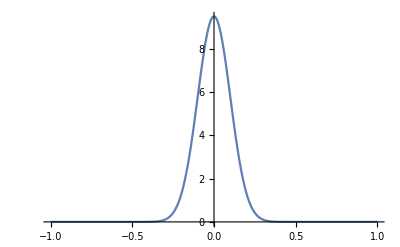

```mathematica
ss=0.1;
strength=4;
gaussian[r_List]:=strength(Pi^(-1/4)ss^(-1/2)Exp[-r[[1]]^2/(2ss^2)]);
Plot[gaussian[{x}],{x,-1,1},PlotRange->All]
newPotential[gaussian];
```

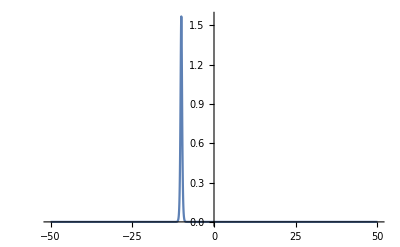

```mathematica
p=3; (* momentum *)
wf=wfshifted*Exp[I p meshX];
ListPlot[projectionX,PlotRange->All,Joined->True]
```

```mathematica
reset;
AbsoluteTiming[evolve["rte",15,50,10]]
```

{60.4215,Null}

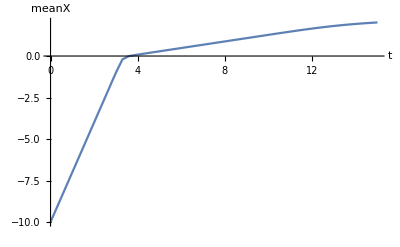

```mathematica
plotM["meanX"]
```

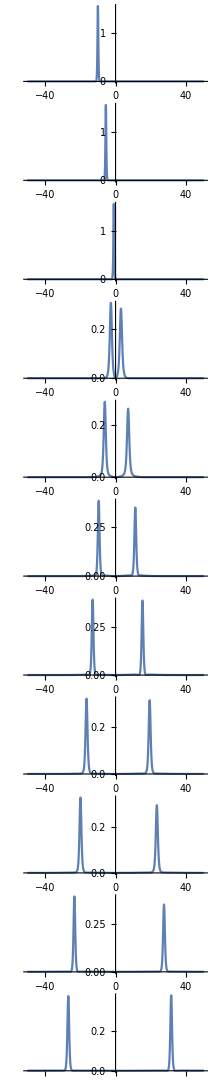

```mathematica
GraphicsGrid[Table[{lplots[[i,2]]},{i,Length[lplots]}],ImageSize->3 72]
```

```mathematica
fitcosh[psi_,min_,max_]:=Module[{tab,fnc,sol,a,b,c},
tab=Table[{x,Abs[psi[x]]^2},{x,min,max,(max-min)/100}];
fnc=(a/Cosh[(x-c)/b])^2;
sol=FindFit[tab,fnc,{{a,1},{b,1},{c,(max+min)/2}},x];
fnc=fnc/.sol;
Print[fnc];
fnc
];
```

0.371309 Sech[1.54429 (26.775+x)]^2

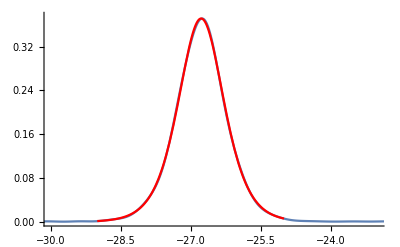

```mathematica
fnc=fitcosh[lplots[[-1,3]],-30,-24];
pfit=Plot[fnc,{x,-29,-25},PlotStyle->Red];
Show[lplots[[-1,2]],pfit,PlotRange->{{-30,-23},All}]
```

0.376033 Sech[1.59262 (-31.5113+x)]^2

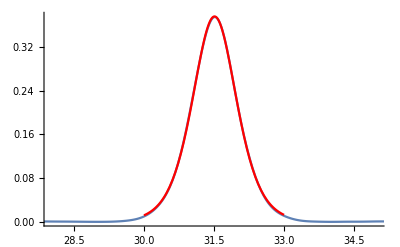

```mathematica
fnc=fitcosh[lplots[[-1,3]],28,35];
pfit=Plot[fnc,{x,30,33},PlotStyle->Red];
Show[lplots[[-1,2]],pfit,PlotRange->{{28,35},All}]
```